```mathematica
PacletDirectoryAdd["~/github/EcoEvo"];
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.7.1 (December 14, 2022)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
VarRangeQ[x_]:=If[ListQ[x]&&Length[x]==3&&NumericQ[x[[2]]]&&NumericQ[x[[3]]],True,False]
```

```mathematica
Unprotect[FindRoots];
Clear[FindRoots];
FindRoots[eqnsin_List,ranges__?VarRangeQ,opts___?OptionQ]:=
Module[{numseeds,method,padding,plotopts,findrootopts,
verbose,verbosity,
(* other variables *)
eqns,dim,roots,seeds,
var,min,max,dvar,vars},

(* set verbosity *)
verbose=Evaluate[Verbose/.Flatten[{opts,Options[FindRoots]}]];
If[verbose,
	verbosity=Max[1,Evaluate[Verbosity/.Flatten[{opts,Options[FindRoots]}]]],
	verbosity=Evaluate[Verbosity/.Flatten[{opts,Options[FindRoots]}]]
];
If[IntegerQ[Global`$verbosity],verbosity=Max[Global`$verbosity,verbosity]];

(* handle options *)
plotopts=Evaluate[PlotOpts/.Flatten[{opts,Options[FindRoots]}]];
findrootopts=Evaluate[FindRootOpts/.Flatten[{opts,Options[FindRoots]}]];
method=Evaluate[Method/.Flatten[{opts,Options[FindRoots]}]];
numseeds=Evaluate[NumSeeds/.Flatten[{opts,Options[FindRoots]}]];
padding=Evaluate[Padding/.Flatten[{opts,Options[FindRoots]}]];

eqns=eqnsin/.(lhs_==rhs_)->rhs-lhs; (* convert equations into functions *)
dim=Length[eqns];
If[dim!=Length[{ranges}],Message[FindRoots::baddim];Abort[]];

deq=-1;
Do[
	{var[i],min[i],max[i]}={ranges}[[i]];
	dvar[i]=(max[i]-min[i]);
	(*Print[i," ",{var[i],min[i],max[i],dvar[i]}];*)
,{i,dim}];
vars=Table[var[i],{i,dim}];

Which[
	method===Random,
	If[numseeds==Automatic,numseeds=10];
	seeds=RandomVariate[UniformDistribution[Table[{min[i],max[i]},{i,dim}]],numseeds]
,
	method===Automatic,
	Which[
		dim==1,
		plot=Plot[Evaluate[eqns/.{var[1]->x}],{x,min[1]-10^-3 dvar[1],max[1]+10^-3 dvar[1]}];
		Print[plot];
		tmp=ExtractPlotPoints[plot][[1]];
		seeds=Mean/@Map[First,Select[Split[tmp,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}]/.{x_?NumericQ->{x}};
	,
		dim==2,
		peqns=Drop[eqns,{deq}];
		plot=ContourPlot[Evaluate[peqns/.{var[1]->x,var[2]->y}],
			{x,min[1]-10^-3 dvar[1],max[1]+10^-3 dvar[1]},{y,min[2]-10^-3 dvar[2],max[2]+10^-3 dvar[2]},
			Contours->{0},ContourShading->False,Evaluate[Sequence@@plotopts]];
		VPrint[3,plot];
		f=Compile[{x,y},Evaluate[eqns[[deq]]/.{var[1]->x,var[2]->y}]];
		seeds=Flatten[Pick[Rest@#,Rest[#]Most[#]&@Sign@Apply[f,#,2],-1]&/@ExtractPlotPoints[plot],1];
	,
		dim==3,
		peqns=Drop[eqns,{deq}];
		plot=ContourPlot3D[Evaluate[peqns/.{var[1]->x,var[2]->y,var[3]->z}],
			{x,min[1]-10^-3 dvar[1],max[1]+10^-3 dvar[1]},{y,min[2]-10^-3 dvar[2],max[2]+10^-3 dvar[2]},{z,min[3]-10^-3 dvar[3],max[3]+10^-3 dvar[3]},
			BoundaryStyle->{1->None,2->None,{1,2}->{}},ContourStyle->None,Mesh->None,
			Evaluate[Sequence@@plotopts]];
		VPrint[3,plot];
		f=Compile[{x,y,z},Evaluate[eqns[[deq]]/.{var[1]->x,var[2]->y,var[3]->z}]];
		seeds=Flatten[Pick[Rest[#],Most[#] Rest[#]&@Sign@Apply[f,#,2],-1]&/@ExtractPlotPoints[plot],1]
	,
		Else,method=Grid
	]
,
	method===Grid,
	If[numseeds==Automatic,numseeds=5];
	If[IntegerQ[numseeds],numseeds=Table[numseeds,{dim}]];
	(*Print["numseeds=",numseeds];*)
	seeds=Tuples[Table[Subdivide[min[i],max[i],numseeds[[i]]-1],{i,dim}]]	
];
VPrint[1,"seeds=",seeds];

If[seeds!={},
	roots=Union[
		Chop[Map[Check[
			FindRoot[eqns,Evaluate[Transpose[{vars,#}]],Evaluate[Sequence@@findrootopts]],Null,{FindRoot::jsing}]&,seeds]]//DeleteNulls,
		SameTest->(RuleListDistance[#1,#2]<10^-8&)
		];
	(*Print["roots=",roots];*)
	Return[Select[roots,And@@Table[min[i]-$MachineEpsilon<=#[[i,2]]<=max[i]+$MachineEpsilon,{i,dim}]&]],
	Return[{}]
];

];
```

```mathematica
Options[FindRoots]={Method->Automatic,NumSeeds->Automatic,FindRootOpts->{},PlotOpts->{},Padding->10^-3,DEq->-1,
Verbose->False,Verbosity->0};
```

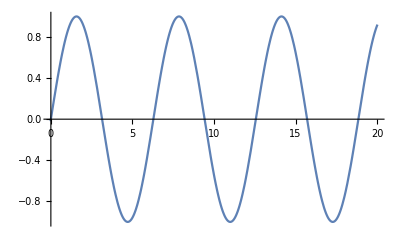

{{x→0},{x→3.14159},{x→6.28319},{x→9.42478},{x→12.5664},{x→15.708},{x→18.8496}}

```mathematica
FindRoots[{Sin[x]},{x,0,20}]
```

```mathematica
FindRoots[{y-x,y+x-1},{x,0,1},{y,0,1}]
```

{{x→0.5,y→0.5}}

```mathematica
FindRoots[{y-x,y+x-1},{x,0,1},{y,0,1},Method->Grid]
```

{{x→0.5,y→0.5}}

```mathematica
FindRoots[{y-x,y+x-1},{x,0,1},{y,0,1},Method->Grid,NumSeeds->10]
```

{{x→0.5,y→0.5}}

```mathematica
FindRoots[{y-x,y+x-1},{x,0,1},{y,0,1},Method->Random]
```

{{x→0.5,y→0.5}}

```mathematica
FindRoots[{y-x,y+x-1},{x,0,1},{y,0,1}]
```

{{x→0.5,y→0.5}}

```mathematica
FindRoots[{y==x,y==1-x},{x,0,1},{y,0,1}]
```

{{x→0.5,y→0.5}}

```mathematica
FindRoots[{x(1-x/4)-x y,x y-y-y z,y z-z},{x,0,4},{y,0,4},{z,0,4}]
```

{{x→0,y→0,z→0},{x→1.,y→0.75,z→0},{x→4.,y→0,z→0}}

```mathematica
FindRoots[{x(1-x/4)-x y,x y-y-y z,y z-z},{x,0,4},{y,0,4},{z,0,4},Method->Grid]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {x,y,z} = {0.,2.,1.}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {x,y,z} = {0.,3.,2.}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {x,y,z} = {0.,4.,3.}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

{{x→0,y→0,z→0},{x→1.,y→0.75,z→0},{x→4.,y→0,z→0}}

```mathematica
FindRoots[{x(1-x/4)-x y,x y-y-y z,y z-z},{x,0,4},{y,0,4},{z,0,4},Method->Random,NumSeeds->100]
```

{{x→0,y→0,z→0},{x→1.,y→0.75,z→0},{x→4.,y→0,z→0}}

```mathematica
FindRoots[{0==x(1-x/4)-x y,0==x y-y-y z,0==y z-z},{x,0,4},{y,0,4},{z,0,4}]
```

{{x→0,y→0,z→0},{x→1.,y→0.75,z→0},{x→4.,y→0,z→0}}